# Plotting of differential equation and curves:

```mathematica
eq = y''[x]+y[x]
```

y[x]+y''[x]

```mathematica
sol = DSolve[eq ==0,y[x],x]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

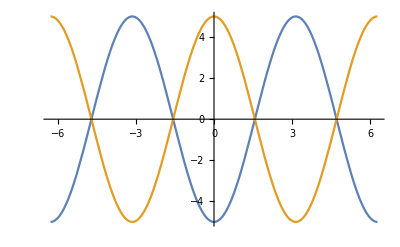

```mathematica
Plot[Evaluate[y[x]/.sol/.{C[2]->0,C[1]->{-5, 5}}],{x,-2Pi,2Pi}]
```

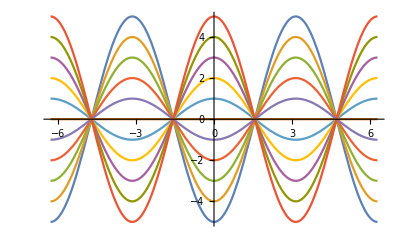

```mathematica
Plot[Evaluate[y[x]/.sol/.{C[2]->0,C[1]->Range[-5,5]}],{x,-2Pi,2Pi}]
```

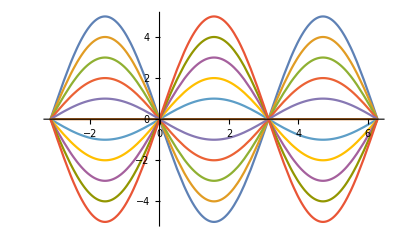

```mathematica
Plot[Evaluate[y[x]/.sol/.{C[1]->0,C[2]->Range[-5,5]}],{x,-Pi,2Pi}]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
eqn = D[y[x],{x,2}]+y[x]
```

y[x]+y''[x]

```mathematica
solution = DSolve[eqn ==0,y[x],x]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

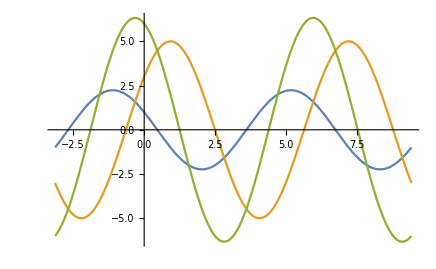

```mathematica
Plot[Evaluate[y[x]/.solution/.{C[1]->{1,3,6},C[2]->{-2,4,-2}}],{x,-Pi,3Pi}]
```

```mathematica
equation = y''[x]+y[x]
```

y[x]+y''[x]

```mathematica
solution = DSolve[{equation==0,y[0]==1,y'[0]==1},y[x],x]
```

{{y[x]→Cos[x]+Sin[x]}}

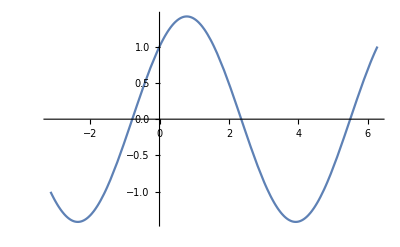

```mathematica
Plot[Evaluate[y[x]/.solution],{x,-Pi,2Pi}]
```

```mathematica
equation = y''[x]+3y'[x]+2y[x]
```

2 y[x]+3 y'[x]+y''[x]

```mathematica
Sol = DSolve[{equation==0,y[0]==1,y'[0]==a},y[x],x]
```

{{y[x]→ⅇ^(-2 x) (-1-a+2 ⅇ^x+a ⅇ^x)}}

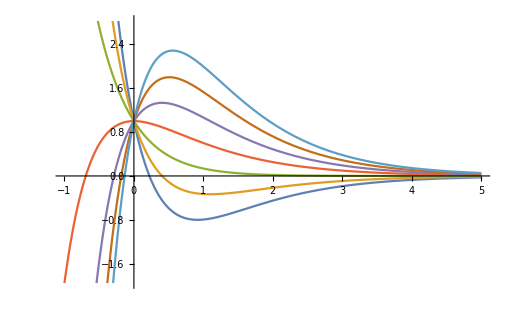

```mathematica
Plot[Evaluate[y[x]/.Sol/.a->{-6,-4,-2,0,2,4,6}],{x,-1,5}]
```

```mathematica
eqn = y''[x] - 2y'[x] + y[x]
```

y[x]-2 y'[x]+y''[x]

```mathematica
solution = DSolve[{eqn ==0, y[0]==3},y[x],x]
```

{{y[x]→ⅇ^x (3+x C[2])}}

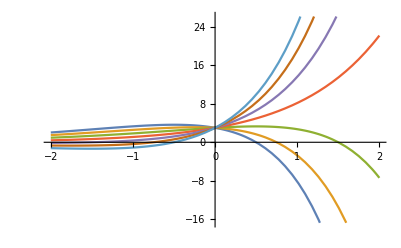

```mathematica
Plot[Evaluate[y[x]/.solution/.C[2]->{-6,-4,-2,0,2,4,6}],{x,-2,2}]
```